```mathematica
(* Rank(Lambda) histogram. (for 5-03-2021) *)
(*  ===================== PARAMS: ===================== *)
n=25
(* =================================================== *)
```

25

```mathematica
(* Stuff: *)
partitionN[r_,m_,n_]:=Module[{r0=r,m0=m,n0=n,counter=0,i,rank,list},
	list = IntegerPartitions[n0];
	Do[rank=Max[list[[i]]]-Length[list[[i]]]; 
	If[Mod[rank,m0]==r0,counter++]; ,{i,Length[list]}];
counter]
PartitionRank[x_]:=First@x-Length@x/;ResourceFunction["IntegerPartitionQ"]@x
```

```mathematica
(* Build set of partitions, compute the rank of each. *)
```

```mathematica
allPartitions = IntegerPartitions[n];
allranks = Table[Abs[PartitionRank[par]],{par,allPartitions}];
```

```mathematica
(* Display Histogram *)
```

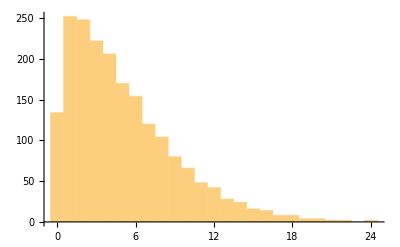

```mathematica
Histogram[allranks]
```